# Superconducting qubits Hub

Set environment, such as threads, gpu, etc.

```mathematica
SetEnvironment["OMP_NUM_THREADS"->"8"]
SetDirectory[NotebookDirectory[]];
```

Load the QuESTLink

```mathematica
Import["/home/cica/programs/QuESTlink/Link/QuESTlink.m"];
CreateLocalQuESTEnv["quest_link_cpu"];
```

Virtual quantum devices, loaded after questlink

```mathematica
Get["../vqd.wl"]
```

frequency unit: MHz
time unit: μs

```mathematica
Options[SuperconductingHub]={
(* The number of qubits should match all assignments. Qubits are numbered from 0 to N-1 *)
qubitsNum->6,
(* The T1 time *)
T1-><|0->63,1->93,2->109,3->115,4->68,5->125|>,
(* The T2 time with Hahn echo applied *)
T2-><|0->113,1->149,2->185,3->161,4->122,5->200|>,
(* Excited population probability in the initialisation, also the thermal state *)
ExcitedInit-><|0->0.032,1->0.021,2->0.008,3->0.009,4->0.025,5->0.007|>,
(* Each qubit frequency in MHz   *)
QubitFreq-><|0->4500,1->4900,2->4700,3->5100,4->4900,5->5300|>,
(* Exchange coupling strength of the resonators. Use [Esc]o-o[Esc] for notation *)
ExchangeCoupling-><|0<->1->4,0<->2->1.5,1<->3->1.5,2<->3->4,2<->4->1.5,3<->5->1.5,4<->5->4|>,
(* Transmon Anharmonicity in MHz *)
Anharmonicity-><|0->296.7,1->298.6,2->297.4,3->298.3,4->297.2,5->299.1|>,
(* Fidelity of qubit readout *)
FidRead-><|0->0.9,1->0.92,2->0.96,3->0.97,4->0.93,5->0.97|>,
(* Measurement duration in μs. It is done without quantum amplifiers *)
DurMeas->5,
(* Duration of the Rx and Ry gates are the same regardless the angle. Rz is virtual and perfect. *)
DurRxRy->0.05,
(* Duration of the cross resonance ZX gate that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZX->0.5,
(* Duration of the sizzle gate is fixed regardless the angle that is fixed regardless the angle. The error is sourced from the passive noise only. *)
DurZZ->0.5,
(* switches to turn/off some noise*)
StdPassiveNoise->True,
ZZPassiveNoise->True
};
```

```mathematica
dev=SuperconductingHub[];
```

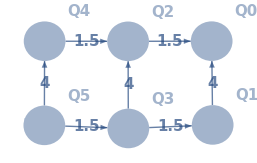

```mathematica
g=dev[Connectivity]
```

## Passive noise

```mathematica
noisycirc=
InsertCircuitNoise[{Subscript[Rx, 0][π],Subscript[Rx, 1][π],Subscript[Rx, 3][π/2],Subscript[ZZ, 1,0],Subscript[ZZ, 4,2],Subscript[ZZ, 4,5],Subscript[Rx, 0][π/4]},SuperconductingHub[]]
```

{{0,{Rx_0[π],Rx_1[π],Rx_3[π/2],ZZ_(4,2)},{Depol_5[0.00299401],Deph_5[0.00124844]}},{0.5,{ZZ_(1,0),ZZ_(4,5)},{Depol_2[0.00343249],Deph_2[0.00134953],Depol_3[0.00325379],Deph_3[0.00155039]}},{1.,{Rx_0[π/4]},{Depol_1[0.000403117],Deph_1[0.000167757],Depol_2[0.000343958],Deph_2[0.000135117],Depol_3[0.000326016],Deph_3[0.000155255],R[-0.0273321,Z_1 Z_3],R[0.133003,Z_2 Z_3],Depol_4[0.000551268],Deph_4[0.000204876],R[-0.0276241,Z_2 Z_4],Depol_5[0.00029994],Deph_5[0.000124984],R[-0.0274045,Z_3 Z_5],R[0.132693,Z_4 Z_5]}}}

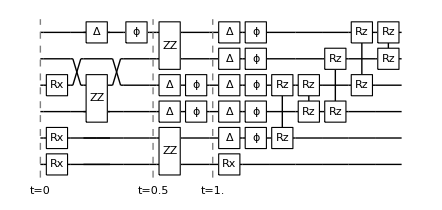

```mathematica
DrawCircuit[noisycirc]
```

## Test the free-induction decays

```mathematica
(* Subscript[ρ, ∞]=p|0X0|+(1-p)|1X1| *)
Subscript[gAmp, q_][γ_,p_]:=Subscript[Kraus, q][{
	Sqrt[p]*{{1,0},{0,Sqrt[1-γ]}},
	Sqrt[p]*{{0,Sqrt[γ]},{0,0}},
	Sequence@@If[p<1, 
	{Sqrt[1-p]*{{Sqrt[1-γ],0},{0,1}},
	Sqrt[1-p]*{{0,0},{Sqrt[γ],0}}},{}]}]
```

```mathematica
ρ=CreateDensityQureg[6];
```

```mathematica
(* excited state population in percent *)
excp={3.2,2.1,0.8,0.9,2.5,0.7};
```

```mathematica
(* probability of output zero *)
initp0=1-0.01*excp
```

{0.968,0.979,0.992,0.991,0.975,0.993}

```mathematica
initmat=KroneckerProduct@@({{#,0},{0,1-#}}&/@initp0);
```

```mathematica
(*** fid: (Tr[Sqrt[ρσ]])^2  ***)
fidDM::usage="fidDM[ρ,σ], ρ=qureq, σ=a density matrix. Fidelity of two density matrices.";
fidDM[ρ_,σ_]:=Re[Tr[MatrixPower[GetQuregMatrix[ρ].σ,1/2]]^2]
```

```mathematica
(* initialise matrix as a random mix state *)
SetQuregMatrix[ρ,RandomMixState[6]];
t1=20;
t2=30;

δt=1;
data=Table[
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-δt/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-δt/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];
{t,fidDM[ρ,initmat]}
,{t,δt,120,δt}];
```

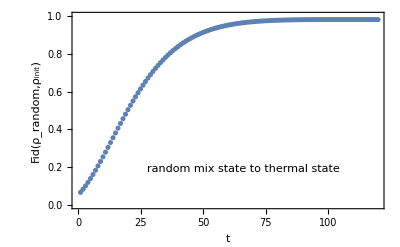

```mathematica
ListPlot[data,PlotRange->{Automatic,{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ_random,ρ_init)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["random mix state to thermal state",Scaled[{0.55,0.2}]]]
```

```mathematica
(* T1 experiment *)
t1=20;
t2=30;
δt=0.5;
dataT1=Table[
ApplyCircuit[InitZeroState@ρ,Subscript[X, #]&/@Range[0,5]];
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-t/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-t/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];
{t,CalcProbOfOutcome[ρ,#,1]}&/@Range[0,5]
,{t,0,120,δt}];
```

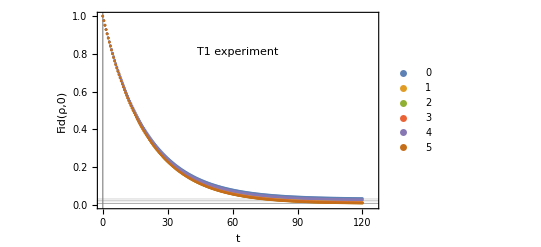

```mathematica
ListPlot[Transpose[dataT1],Frame->True,PlotLegends->Range[0,5],GridLines->{excp*0.01},PlotRange->{{0,125},{0,1}},Frame->True,FrameLabel->{"t","Fid(ρ,0)"},FrameStyle->Directive[Black,Thick],ImageSize->400,BaseStyle->{17},Epilog->Inset["T1 experiment",Scaled[{0.5,0.8}]]]
```

```mathematica
(* T2 experiment *)
t1=20;
t2=30;
δt=1;
dataT2=Table[
ApplyCircuit[InitZeroState@ρ,Subscript[H, #]&/@Range[0,5]];
t1decay=Subscript[gAmp, #-1][(1-ⅇ^(-t/t1)),initp0[[#]]]&/@Range[6];
t2decay=Subscript[Deph, #][(1-ⅇ^(-t/t2))0.5]&/@Range[0,5];
ApplyCircuit[ρ,Join[t1decay,t2decay]];

ApplyCircuit[ρ,Subscript[H, #]&/@Range[0,5]];
{t,CalcProbOfOutcome[ρ,#,0]}&/@Range[0,5]
,{t,0,120,δt}];
```

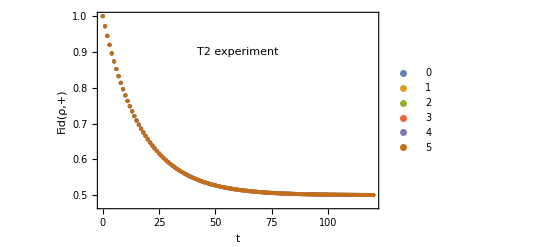

```mathematica
ListPlot[Transpose[dataT2],PlotLegends->Placed[Range[0,5],{0.9,0.5}],PlotRange->All,Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->400,FrameLabel->{"t","Fid(ρ,+)"},BaseStyle->{17},Epilog->Inset["T2 experiment",Scaled[{0.5,0.8}]]]
```